```mathematica
bindleft[leftsin_,rightsin_,numbind_]:=Module[{rand,lefts = leftsin,rights = rightsin},
		 rand =RandomInteger[{1,Length[lefts]}];
				If[lefts[[rand]]>numbind actinpertrop+1 && (rand==1||lefts[[rand]]>rights[[rand -1]]+numbind actinpertrop),
				lefts[[rand]]+=-numbind actinpertrop;
				If[rand>1,
				If[lefts[[rand]]==rights[[rand -1]]+1,
				rights[[rand-1]] = rights[[rand]];
				lefts = Delete[lefts,rand];
				rights = Delete[rights,rand];
				]];];
{lefts,rights}
];
bindright[leftsin_,rightsin_,numbind_]:=Module[{rand,lefts = leftsin,rights = rightsin},
		 rand =RandomInteger[{1,Length[rights]}];
				If[rights[[rand]]<totallength+1-numbind actinpertrop&&(rand==Length[rights]||lefts[[rand+1]]>rights[[rand]]+numbind actinpertrop),
				rights[[rand]]+=numbind actinpertrop;
				If[rand<Length[lefts],
				If[lefts[[rand+1]]==rights[[rand]]+1,
				rights[[rand]] = rights[[rand+1]];
				lefts = Delete[lefts,rand+1];
				rights = Delete[rights,rand+1];
				]];];
{lefts,rights}
];
decayleft[leftsin_,rightsin_,numbind_]:=Module[{rand,lefts = leftsin,rights = rightsin},
		 rand =RandomInteger[{1,Length[lefts]}];
			(*lefts[[rand]]+=numbind actinpertrop;
			If[lefts[[rand]]>rights[[rand]],
				lefts = Delete[lefts,rand];
				rights = Delete[rights,rand];
			];*)
		If[lefts[[rand]]+numbind actinpertrop≤ rights[[rand]],
			lefts[[rand]]+=numbind actinpertrop;];
{lefts,rights}
];
decayright[leftsin_,rightsin_,numbind_]:=Module[{rand,lefts = leftsin,rights = rightsin},
		 rand =RandomInteger[{1,Length[rights]}];
			(*rights[[rand]]+=-numbind actinpertrop;
			If[lefts[[rand]]>rights[[rand]],
				lefts = Delete[lefts,rand];
				rights = Delete[rights,rand];,
			];*)
			If[lefts[[rand]]≤ rights[[rand]]-numbind actinpertrop,
				rights[[rand]]+=-numbind actinpertrop;];
{lefts,rights}
];

nucleation[leftsin_,rightsin_,numbind_]:=Module[{rand,pos,next,lefts = leftsin,rights = rightsin},
		 rand =RandomInteger[{1,(totallength-numbound)}];
			pos=0;
			next = 1;
			Do[pos++;While[next≤ Length[lefts] &&pos≥ lefts[[next]],pos+=rights[[next]]-lefts[[next]]+1;next++],{i,1,rand}];
			If[(Length[lefts]<next && pos<=totallength-numbind actinpertrop+1)||(Length[lefts]≥next && pos+numbind actinpertrop-1<lefts[[next]]),
			lefts = Insert[lefts,pos,next];
			rights = Insert[rights,pos+numbind actinpertrop-1,next];
			rand = next;
			If[rand>1,
				If[lefts[[rand]]==rights[[rand -1]]+1,
				rights[[rand-1]] = rights[[rand]];
				lefts = Delete[lefts,rand];
				rights = Delete[rights,rand];
				rand+=-1;
			]];
			If[rand<Length[lefts],
				If[lefts[[rand+1]]==rights[[rand]]+1,
				rights[[rand]] = rights[[rand+1]];
				lefts = Delete[lefts,rand+1];
				rights = Delete[rights,rand+1];
				]];];
{lefts,rights}
];

releasetrop[leftsin_,rightsin_,lengthsin_,cutoff_]:=Module[{rand,lefts = leftsin,rights = rightsin,allpos},
		allpos = Flatten[Position[lengthsin,_?(#== cutoff &)]];
		 rand =allpos[[RandomInteger[{1,Length[allpos]}]]];
				lefts = Delete[leftsin,rand];
				rights = Delete[rights,rand];

{lefts,rights}
];
```

```mathematica
umtomon = 30.3;
actinpertrop = 1;
maxtime =200*60;
filamentlength =8;
```

```mathematica
(*successful nucleation probability*)
sols = Table[concentration =conin;


successfulnucs=ParallelTable[

growthrateleft1 = concentration 0.02;

growthrateright1 =concentration 0.037;

decayrateleft1=  0.033;

decayrateright1=   0.061;

nucleationrate1 =concentration 0.0000155; 

release1 = 1.25;

totallength = Ceiling[actinpertrop umtomon filamentlength];
probs=Table[0,{6}];
       lefts = {};
rights = {};
lengths = rights-lefts+1;

	t=0;

kymograph={};
prevouttab = Table[0,{totallength}];
While[t<maxtime+0.5,
numbound = Total[lengths];
probs[[1]] = growthrateleft1 Length[lefts];

probs[[2]] = growthrateright1 Length[rights];

probs[[3]]= nucleationrate1(totallength-numbound);

probs[[4]]= decayrateleft1 Length[lefts];

probs[[5]]= decayrateright1 Length[rights];

probs[[6]] =release1 Length[Position[lengths,_?(#==1 &)]];


totalprob = Total[probs];

deltat =  -1/totalprob Log[1-RandomReal[]];
t+=deltat;
rand = RandomReal[];
If[rand<probs[[1]]/totalprob,(*bind left*)
{lefts,rights} = bindleft[lefts,rights,1];
,rand+=-probs[[1]]/totalprob;If[rand<probs[[2]]/totalprob,(*bind right*)
{lefts,rights} = bindright[lefts,rights,1];
,rand+=-probs[[2]]/totalprob;If[rand<probs[[3]]/totalprob,(*nucleation*)
{lefts,rights} = nucleation[lefts,rights,1];
,rand+=-probs[[3]]/totalprob;If[rand<probs[[4]]/totalprob,(*decay right*)
{lefts,rights} = decayleft[lefts,rights,1];
,rand+=-probs[[4]]/totalprob;If[rand<probs[[5]]/totalprob,(*decay right*)
{lefts,rights} = decayright[lefts,rights,1];
,rand+=-probs[[5]]/totalprob;If[rand<probs[[6]]/totalprob,(*monomer release*)
{lefts,rights} = releasetrop[lefts,rights,lengths,1];

]]]]]];
lengths =rights-lefts+1;
numbound = Total[lengths];
If[Floor[t-deltat]<Floor[t],
outtab = Table[0,{totallength}];
Do[outtab[[lefts[[i]]+j-1]]=1,{i,1,Length[lefts]},{j,1,lengths[[i]]}];
Do[AppendTo[kymograph,prevouttab];,{Min[Floor[t]-Floor[t-deltat]-1,maxtime-Length[kymograph]]}];
If[Length[kymograph]<maxtime,AppendTo[kymograph,outtab];];
prevouttab = outtab;
];
If[numbound>0.9 totallength,Break[]];
];
Quiet[firstnuc = Dimensions[kymograph][[1]]-Check[ComponentMeasurements[DeleteSmallComponents[MorphologicalComponents[Image[kymograph]],2000],"BoundingBox"][[1,2,2,2]],0];];
firstnuc
,{countout,1, 10000}];
lev2nucs =10^-6 filamentlength Sort[ Min[#]&/@successfulnucs,Greater];
	cdf =Transpose[{lev2nucs,Range[Length[lev2nucs]]}];
	trimmedcdf = Select[cdf,0.90*Max[cdf[[All,2]]]>#[[2]]&&#[[1]]<0.99*Max[cdf[[All,1]]] &];
	expfit =FindFit[trimmedcdf,A E^(-b frame),{{A,Length[successfulnucs] },{b,3/Max[cdf[[All,1]]]}},frame];
	model = A E^(-b frame)/.expfit;
	fitoverlay = Show[ListLinePlot[cdf,PlotStyle->Thick,PlotRange->{0,All},AxesOrigin->{0,0}],Plot[model,{frame,0,Max[cdf[[All,1]] ]},PlotStyle->Red,PlotRange->All]];
	rate = b/.expfit;
	halflife = N[Log[2]]/rate;
Print[{concentration,rate}];
{fitoverlay,concentration,rate,halflife,cdf},{conin,3,20,0.5}];
```

{3.,82.1218}

{3.5,124.833}

{4.,180.512}

{4.5,235.849}

{5.,302.337}

{5.5,380.321}

{6.,465.058}

{6.5,532.667}

{7.,638.028}

{7.5,737.911}

{8.,813.753}

{8.5,944.843}

{9.,1061.2}

{9.5,1170.}

{10.,1294.82}

{10.5,1382.15}

{11.,1515.44}

{11.5,1691.32}

{12.,1764.84}

{12.5,1945.87}

{13.,2067.19}

{13.5,2228.46}

{14.,2332.44}

{14.5,2449.03}

{15.,2619.36}

{15.5,2812.59}

{16.,2937.51}

{16.5,3124.57}

{17.,3214.45}

{17.5,3394.89}

{18.,3552.26}

{18.5,3787.65}

{19.,3884.72}

{19.5,4113.05}

{20.,4252.58}

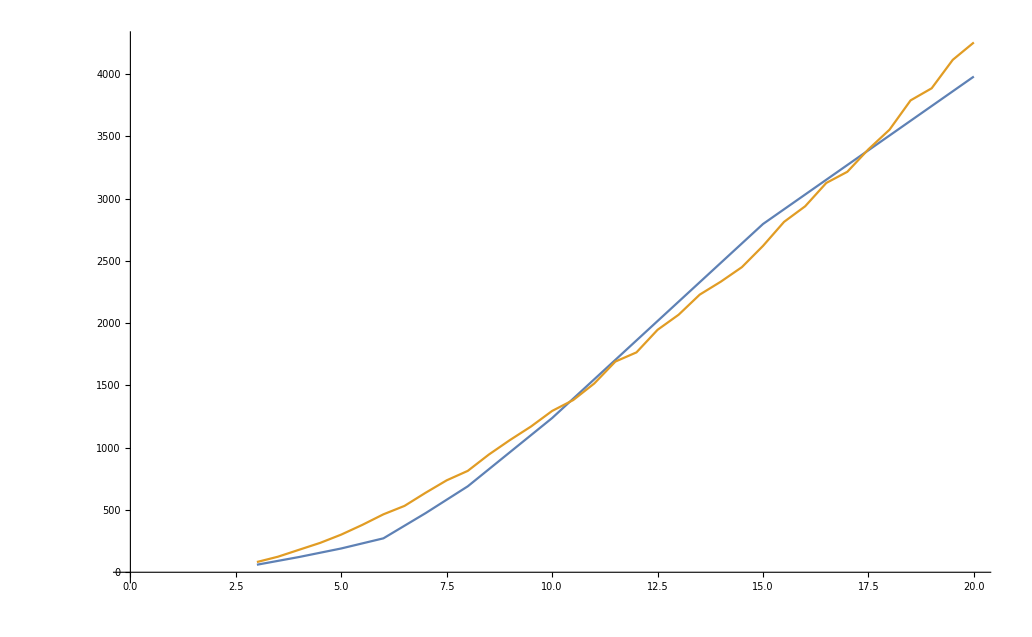

```mathematica
ListLinePlot[{allcontofito,{#[[2]],#[[3]]}&/@sols}]
```

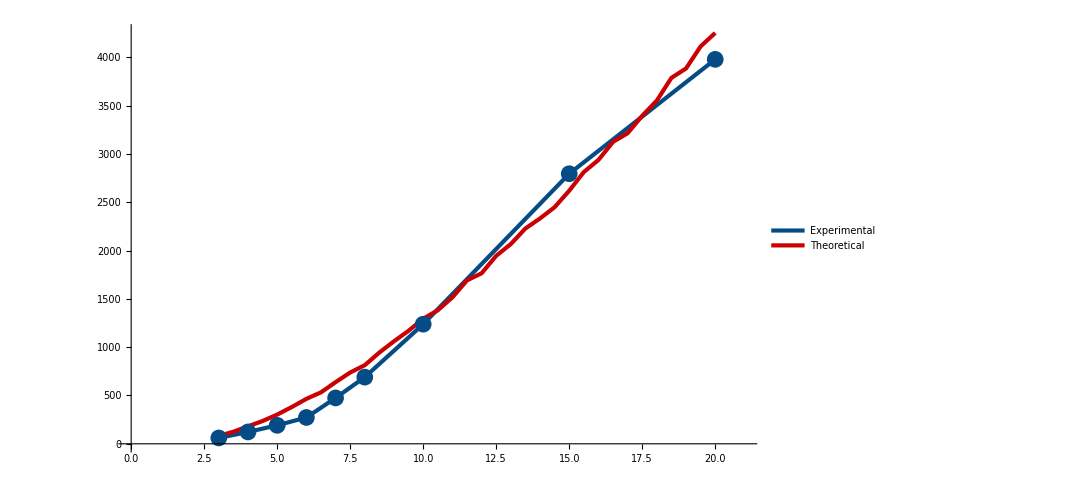
-Graphics-Nucleation Rate (m^-1 s^-1)Concentration (nM)

```mathematica
toout = Labeled[Show[{ListLinePlot[{allcontofito,{#[[2]],#[[3]]}&/@sols},PlotRange->{{0,21},{0,All}},PlotStyle->{{colors[[2]],AbsoluteThickness[3]},{colors[[1]],AbsoluteThickness[3]}},AxesStyle->{{Black,Thick,FontFamily->"Helvetica",Large},{Black,Thick,FontFamily->"Helvetica",Large}},TicksStyle->Black,PlotLegends->Placed[{Style["Experimental",{Black,18,Bold,FontFamily->"Helvetica"}],Style["Theoretical",{Black,18,Bold,FontFamily->"Helvetica"}]},{{0.25,0.7}}]],ListPlot[{#[[1]],#[[2]]}&/@allcontofito,PlotStyle->{{colors[[2]],PointSize[0.015]}}]},ImageSize->800],{Rotate[Style["Nucleation Rate (m^-1 s^-1)",{Black,20,Bold,FontFamily->"Helvetica"}],π/2],Style["Concentration (nM)",{Black,20,Bold,FontFamily->"Helvetica"}]},{Left,Bottom}]
```

```mathematica
Export["C:\\Users\\James_Walsh\\Dropbox\\Tropomyosin_Analysis\\New_Figures\\Modelling\\Nucleation_theory_exp_overlay.eps",toout];
Export["C:\\Users\\James_Walsh\\Dropbox\\Tropomyosin_Analysis\\New_Figures\\Modelling\\Nucleation_theory_exp_overlay.png",toout,ImageResolution->200];
```

```mathematica
umtomon = 1000/33;
actinpertrop = 1;
maxtime =200*60;
filamentlength =8;
```

```mathematica
(*successful nucleation probability*)
sols = Table[concentration =conin;


successfulnucs=ParallelTable[

growthrateleft1 = concentration 0.01945;

growthrateright1 =concentration 0.036;

decayrateleft1= 0.0325;

decayrateright1=   0.06;

nucleationrate1 =concentration 0.0000155; 

release1 = 1.25;

totallength = Ceiling[actinpertrop umtomon filamentlength];
probs=Table[0,{6}];
       lefts = {};
rights = {};
lengths = rights-lefts+1;

	t=0;

kymograph={};
prevouttab = Table[0,{totallength}];
While[t<maxtime+0.5,
numbound = Total[lengths];
probs[[1]] = growthrateleft1 Length[lefts];

probs[[2]] = growthrateright1 Length[rights];

probs[[3]]= nucleationrate1(totallength-numbound);

probs[[4]]= decayrateleft1 Length[lefts];

probs[[5]]= decayrateright1 Length[rights];

probs[[6]] =release1 Length[Position[lengths,_?(#==1 &)]];


totalprob = Total[probs];

deltat =  -1/totalprob Log[1-RandomReal[]];
t+=deltat;
rand = RandomReal[];
If[rand<probs[[1]]/totalprob,(*bind left*)
{lefts,rights} = bindleft[lefts,rights,1];
,rand+=-probs[[1]]/totalprob;If[rand<=probs[[2]]/totalprob,(*bind right*)
{lefts,rights} = bindright[lefts,rights,1];
,rand+=-probs[[2]]/totalprob;If[rand<=probs[[3]]/totalprob,(*nucleation*)
{lefts,rights} = nucleation[lefts,rights,1];
,rand+=-probs[[3]]/totalprob;If[rand<=probs[[4]]/totalprob,(*decay right*)
{lefts,rights} = decayleft[lefts,rights,1];
,rand+=-probs[[4]]/totalprob;If[rand<=probs[[5]]/totalprob,(*decay right*)
{lefts,rights} = decayright[lefts,rights,1];
,rand+=-probs[[5]]/totalprob;If[rand<=probs[[6]]/totalprob,(*monomer release*)
{lefts,rights} = releasetrop[lefts,rights,lengths,1];

]]]]]];
lengths =rights-lefts+1;
numbound = Total[lengths];
If[Floor[t-deltat]<Floor[t],
outtab = Table[0,{totallength}];
Do[outtab[[lefts[[i]]+j-1]]=1,{i,1,Length[lefts]},{j,1,lengths[[i]]}];
Do[AppendTo[kymograph,prevouttab];,{Min[Floor[t]-Floor[t-deltat]-1,maxtime-Length[kymograph]]}];
If[Length[kymograph]<maxtime,AppendTo[kymograph,outtab];];
prevouttab = outtab;
];
If[numbound>0.9 totallength,Break[]];
];
pos =Select[If[Min[#]>0,1, Position[#,0][[-1,1]]+1]&/@Take[Transpose[DeleteSmallComponents[MorphologicalComponents[kymograph]]],{20,220}],#<0.99 Length[kymograph] &];
	peaks = N[FindPeaks[pos,5]];
	troughs =N[{#[[1]],-#[[2]]}]&/@ FindPeaks[-pos,5];
	allpeaks = {Mean[#[[All,1]]],Mean[#[[All,2]]]}&/@Split[Sort[Join[{#[[1]],#[[2]],True}&/@troughs,{#[[1]],#[[2]],False}&/@peaks],#1[[1]]<#2[[1]] &],#1[[3]]==#2[[3]] &];
	(*grad = Table[(allpeaks[[i+1,1]]-allpeaks[[i,1]])/(allpeaks[[i+1,2]]-allpeaks[[i,2]]+0.0000000000000001),{i,1,Length[allpeaks]-1}]*)
xvals = Round[allpeaks[[All,1]]];
grad=Table[Quiet[Check[1/ LinearModelFit[Take[pos,{xvals[[i]]+1,xvals[[i+1]]-1}],x,x]["BestFitParameters"][[2]],0]],{i,1,Length[xvals]-1}]
,{countout,1, 1000}];
posgrads = Select[Flatten[successfulnucs],1># && #>0.0000001 &];
cdf = Transpose[{Sort[posgrads],N[(Range[Length[posgrads]]-1)/(Length[posgrads]-1)]}];
posfit ={x0,σ}/. FindFit[cdf,1/2(1+Erf[(x-x0)/(Sqrt[2]σ)]),{{x0,Mean[posgrads]},σ},x];
posstats = {Median[posgrads],StandardDeviation[posgrads]};
posgrads = -Select[Flatten[successfulnucs],-1<# && #<-0.0000001 &];
cdf = Transpose[{Sort[posgrads],N[(Range[Length[posgrads]]-1)/(Length[posgrads]-1)]}];
negfit ={x0,σ}/. FindFit[cdf,1/2(1+Erf[(x-x0)/(Sqrt[2]σ)]),{{x0,Mean[posgrads]},σ},x];
negstats = {Median[posgrads],StandardDeviation[posgrads]};
Print[{conin,posfit,negfit,posstats,negstats}];
{conin,posfit,negfit,posstats,negstats},{conin,2.5,10,0.5}];
```

{2.5,{0.0329742,0.0101214},{0.0184377,0.00624423},{0.0322234,0.0148127},{0.0181004,0.0119992}}

{3.,{0.0516795,0.0140284},{0.0290806,0.00882585},{0.0511826,0.0204446},{0.028688,0.0297183}}

{3.5,{0.069796,0.0171083},{0.0387792,0.0113422},{0.0690068,0.0215981},{0.0384344,0.020068}}

{4.,{0.0885517,0.0212982},{0.0487031,0.0131169},{0.0879223,0.0268376},{0.0482537,0.0325178}}

{4.5,{0.106688,0.0241276},{0.0596957,0.016},{0.105816,0.0350889},{0.0590049,0.0356889}}

{5.,{0.124244,0.0277142},{0.0693251,0.0186209},{0.123666,0.0366546},{0.0681306,0.0265221}}

{5.5,{0.143545,0.0308435},{0.0796711,0.0214426},{0.142907,0.040512},{0.0789092,0.0354856}}

{6.,{0.162677,0.0345756},{0.0904394,0.0229046},{0.160835,0.046407},{0.0899737,0.0373311}}

{6.5,{0.180913,0.0363852},{0.101028,0.0261658},{0.179866,0.0472667},{0.0998467,0.0439882}}

{7.,{0.197741,0.0407751},{0.111891,0.0292776},{0.196371,0.0582346},{0.110716,0.0494028}}

{7.5,{0.217732,0.0469104},{0.121024,0.030625},{0.216107,0.0590658},{0.119464,0.0489525}}

{8.,{0.235985,0.0476791},{0.132385,0.0338388},{0.234915,0.0590274},{0.131112,0.0516995}}

{8.5,{0.258488,0.0527234},{0.143025,0.0358451},{0.256681,0.0671503},{0.142046,0.0621292}}

{9.,{0.27274,0.0589072},{0.153029,0.0394129},{0.27027,0.0795289},{0.150897,0.0544275}}

{9.5,{0.292249,0.0619915},{0.163586,0.0409382},{0.290488,0.0727802},{0.162235,0.0622032}}

{10.,{0.310766,0.0615395},{0.1729,0.0427256},{0.309134,0.0781856},{0.169881,0.0657762}}

```mathematica
Differences[xvals]
```

{28,12,49,50}

```mathematica
pos
```

{496,496,488,485,482,479,465,459,455,433,419,419,405,404,399,396,394,391,391,378,376,375,371,370,363,356,354,353,341,339,339,341,343,344,344,348,351,352,354,359,362,367,366,361,358,356,351,350,345,344,335,331,321,317,304,303,302,297,297,297,285,284,273,268,266,265,265,262,261,259,249,248,240,236,205,205,183,144,139,138,136,127,119,114,110,105,105,102,101,98,53,64,68,75,77,81,81,81,84,92,99,106,110,110,115,126,128,132,133,135,136,137,141,146,147,148,149,150,165,166,169,170,172,174,176,178,185,188,191,194,194,196,197,197,199,205,222,223,224,227,232}

```mathematica
xvals = Round[allpeaks[[All,1]]];
```

```mathematica
grad=Table[ LinearModelFit[Take[pos,{xvals[[i]]+1,xvals[[i+1]]-1}],x,x]["BestFitParameters"][[2]],{i,1,Length[xvals]-1}];
```

```mathematica
LinearModelFit[tofit,x,x]["BestFitParameters"][[2]]
```

-5.58669

```mathematica
grad
```

{-5.41379,2.43478,-6.40816,3.58}

```mathematica
Needs["ErrorBarPlots`"];
colors =  {RGBColor[({228,26,28}-26)/255],RGBColor[({55,126,184}-50)/255],RGBColor[{77,175,74}/255],RGBColor[{253,174,97}/255],RGBColor[{200,0,0}/255],RGBColor[{152,78,163}/255],RGBColor[{0,128,0}/255],Magenta}
```

ErrorBar::shdw: Symbol ErrorBar appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts {ErrorBarPlots`,Global`}; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

{RGBColor[{Rational[202, 255], 0, Rational[2, 255]}],RGBColor[{Rational[1, 51], Rational[76, 255], Rational[134, 255]}],RGBColor[{Rational[77, 255], Rational[35, 51], Rational[74, 255]}],RGBColor[{Rational[253, 255], Rational[58, 85], Rational[97, 255]}],RGBColor[{Rational[40, 51], 0, 0}],RGBColor[{Rational[152, 255], Rational[26, 85], Rational[163, 255]}],RGBColor[{0, Rational[128, 255], 0}],RGBColor[1, 0, 1]}

```mathematica
toplot ={#[[1]], 33 #[[4,1]]}&/@sols;
err = ErrorBar[#]&/@(33 sols[[All,4,2]]);
plot1 = ErrorListPlot[Transpose[{toplot,err}],PlotRange->{{-0.1,10.5},{-3,14}},PlotStyle->colors[[2]],AxesStyle->{{Black,Thick,FontFamily->"Helvetica",Large},{Black,Thick,FontFamily->"Helvetica",Large}},TicksStyle->Black];
```

```mathematica
toplot2 ={#[[1]],33 #[[5,1]]}&/@sols;
err2 = ErrorBar[#]&/@(33 sols[[All,5,2]]);
plot2 = ErrorListPlot[Transpose[{toplot2,err2}],PlotRange->{{0,10.5},{-3,11}},PlotStyle->colors[[1]]];
```

```mathematica
fit = (-1.0735144482714267-1.9836657474276236 ⅈ)+(0.6421546169324674+1.1865887042438488 ⅈ) x;
fitplot = Plot[{Re[fit],Im[fit]},{x,0,11},PlotStyle->{{colors[[1]],AbsoluteThickness[3]},{colors[[2]],AbsoluteThickness[3]},{colors[[4]],AbsoluteThickness[3]},{colors[[3]],AbsoluteThickness[3]}},PlotLegends->Placed[{Style["Pointed End",{Black,18,Bold,FontFamily->"Helvetica"}],Style["Barbed End",{Black,18,Bold,FontFamily->"Helvetica"}]},{{0.25,0.8}}],LabelStyle->Medium];
```

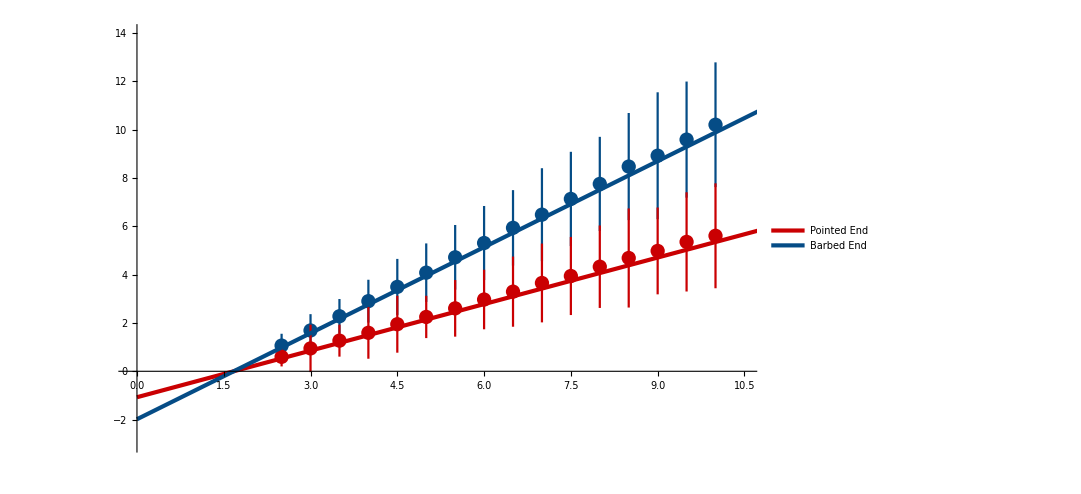
-Graphics-k_growth(nm/s)Concentration (nM)

```mathematica
toout = Labeled[Show[{plot1,plot2,fitplot},ImageSize->800],{Rotate[Style["k_growth(nm/s)",{Black,20,Bold,FontFamily->"Helvetica"}],π/2],Style["Concentration (nM)",{Black,20,Bold,FontFamily->"Helvetica"}]},{Left,Bottom,Top}]
```

```mathematica
fit = (-1.0735144482714267-1.9836657474276236 ⅈ)+(0.6421546169324674+1.1865887042438488 ⅈ) x;
theoryfit = FindFit[{#[[1]], 33 #[[5,1]]+I 33 #[[4,1]]}&/@sols,a+b x+c I+(b c/a )I x,{{a,-1.2},{b,0.67},{c,-2.3}},x,NormFunction->(Norm[#1,1]&)];
theoryfit=a+b x+c I+(b c/a )I x/.theoryfit
```

(-1.0993-1.97555 ⅈ)+(0.67641+1.21558 ⅈ) x

```mathematica
polrates1 ={{0,-0.9940905887982523},{3,0.7652898023881713},{4,1.610657848219595},{5,1.8293858235511589},{6,2.735420107012019},{7,3.102453748351272},{8,4.214712765491353},{10,5.642183713859733}};
```

```mathematica
polrates2 = {{0,-2.144515956906309},{3,1.7341248269583438},{4,2.8671924415860004},{5,3.40251448901759},{6,5.2327816606358155},{7,5.831062361283114},{8,8.16828180768245},{10,9.433919825322626}};
```

```mathematica
pointplot = ListPlot[{{#[[1]], 33 #[[4,1]]}&/@sols,{#[[1]],33 #[[5,1]]}&/@sols,polrates2,polrates1},PlotStyle->{{colors[[3]],PointSize[0.015]},{colors[[4]],PointSize[0.015]},{colors[[2]],PointSize[0.015]},{colors[[1]],PointSize[0.015]}}];
```

```mathematica
fitplot = Plot[{Re[fit],Im[fit],Re[theoryfit],Im[theoryfit]},{x,0,11},PlotStyle->{{colors[[1]],AbsoluteThickness[3]},{colors[[2]],AbsoluteThickness[3]},{colors[[4]],AbsoluteThickness[3]},{colors[[3]],AbsoluteThickness[3]}},PlotLegends->Placed[{Style["Pointed End Experiment",{Black,30,Bold,FontFamily->"Helvetica"}],Style["Barbed End Experiment",{Black,30,Bold,FontFamily->"Helvetica"}],Style["Pointed End Model",{Black,30,Bold,FontFamily->"Helvetica"}],Style["Barbed End Model",{Black,30,Bold,FontFamily->"Helvetica"}]},{{0.35,0.75}}],LabelStyle->Large,AxesStyle->{{Black,Thick,FontFamily->"Helvetica",30},{Black,Thick,FontFamily->"Helvetica",30}},TicksStyle->Black,ImageSize->650];
```

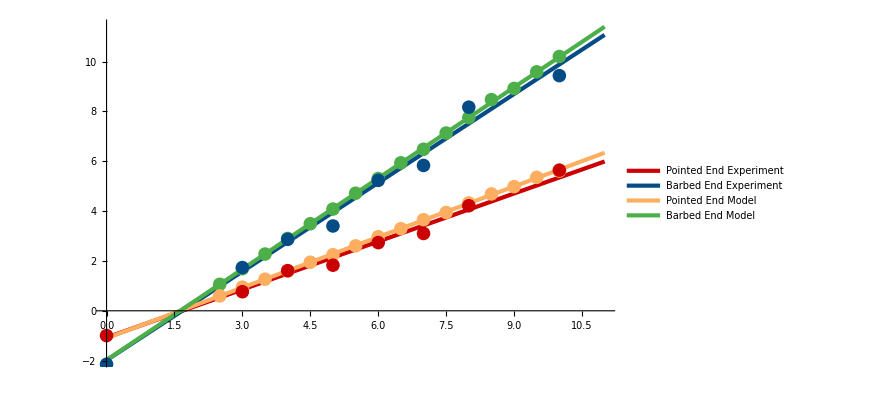
-Graphics-k_growth(nm/s)Concentration (nM)

```mathematica
toout = Labeled[Show[{fitplot,pointplot}],{Rotate[Style["k_growth(nm/s)",{Black,30,Bold,FontFamily->"Helvetica"}],π/2],Style["Concentration (nM)",{Black,30,Bold,FontFamily->"Helvetica"}]},{Left,Bottom,Top}]
```

```mathematica
Export["C:\\Users\\James_Walsh\\Dropbox\\Tropomyosin_Analysis\\New_Figures\\Modelling\\Model_Growthrate_Overlayv2.eps",toout];
Export["C:\\Users\\James_Walsh\\Dropbox\\Tropomyosin_Analysis\\New_Figures\\Modelling\\Model_Growthrate_Overlayv2.png",toout,ImageResolution->200];
```

```mathematica
toplot ={#[[1]], 33 #[[4,1]]}&/@sols;
err = ErrorBar[#]&/@(33 sols[[All,4,2]]);
plot1 = ErrorListPlot[Transpose[{toplot,err}],PlotRange->{{-0.1,10.5},{-3,14}},PlotStyle->colors[[2]],AxesStyle->{{Black,Thick,FontFamily->"Helvetica",Large},{Black,Thick,FontFamily->"Helvetica",Large}},TicksStyle->Black];
```

```mathematica
toplot2 ={#[[1]],33 #[[5,1]]}&/@sols;
err2 = ErrorBar[#]&/@(33 sols[[All,5,2]]);
plot2 = ErrorListPlot[Transpose[{toplot2,err2}],PlotRange->{{0,10.5},{-3,11}},PlotStyle->colors[[1]]];
```

```mathematica
fit = (-1.0735144482714267-1.9836657474276236 ⅈ)+(0.6421546169324674+1.1865887042438488 ⅈ) x;
fitplot = Plot[{Re[fit],Im[fit]},{x,0,11},PlotStyle->{{colors[[1]],AbsoluteThickness[3]},{colors[[2]],AbsoluteThickness[3]},{colors[[4]],AbsoluteThickness[3]},{colors[[3]],AbsoluteThickness[3]}},PlotLegends->Placed[{Style["Pointed End",{Black,18,Bold,FontFamily->"Helvetica"}],Style["Barbed End",{Black,18,Bold,FontFamily->"Helvetica"}]},{{0.25,0.8}}],LabelStyle->Medium];
```

```mathematica
toout = Labeled[Show[{plot1,plot2,fitplot},ImageSize->800],{Rotate[Style["k_growth(nm/s)",{Black,20,Bold,FontFamily->"Helvetica"}],π/2],Style["Concentration (nM)",{Black,20,Bold,FontFamily->"Helvetica"}]},{Left,Bottom,Top}]
```

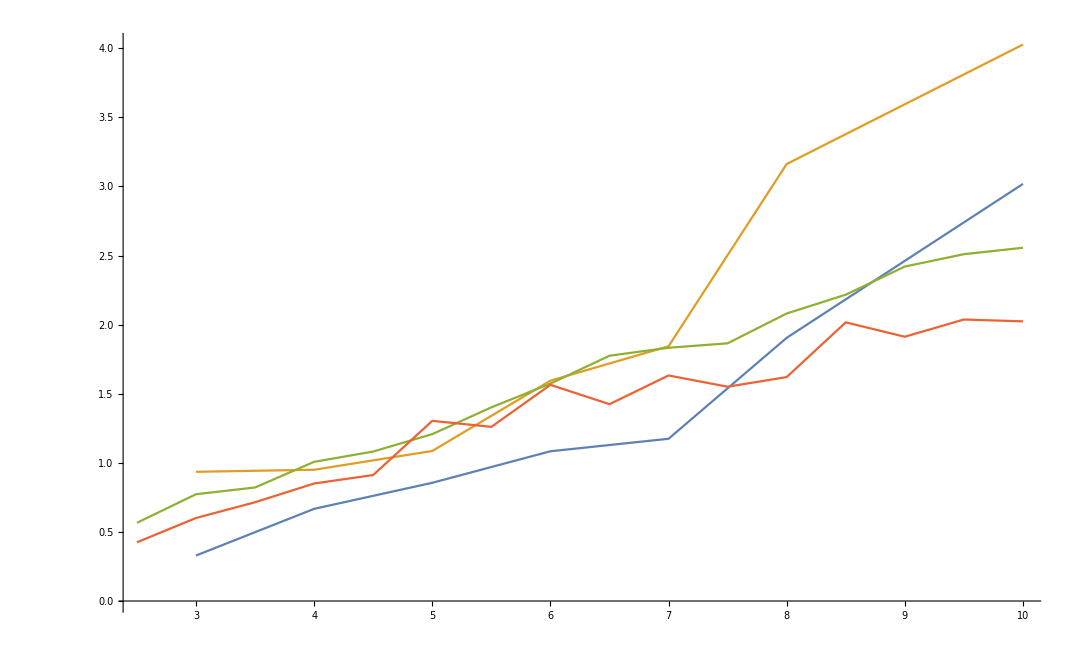

```mathematica
toplot = Drop[Transpose[{con2,rates[[All,7]]}],{2,3}];
toplot2 = Drop[Transpose[{con2,rates[[All,8]]}],{2,3}];
toplot3 ={#[[1]], 33 #[[4,2]]}&/@sols;
toplot4={#[[1]], 33 #[[5,2]]}&/@sols;

ListLinePlot[Sort[#]&/@{toplot,toplot2,toplot3,toplot4 }]
```

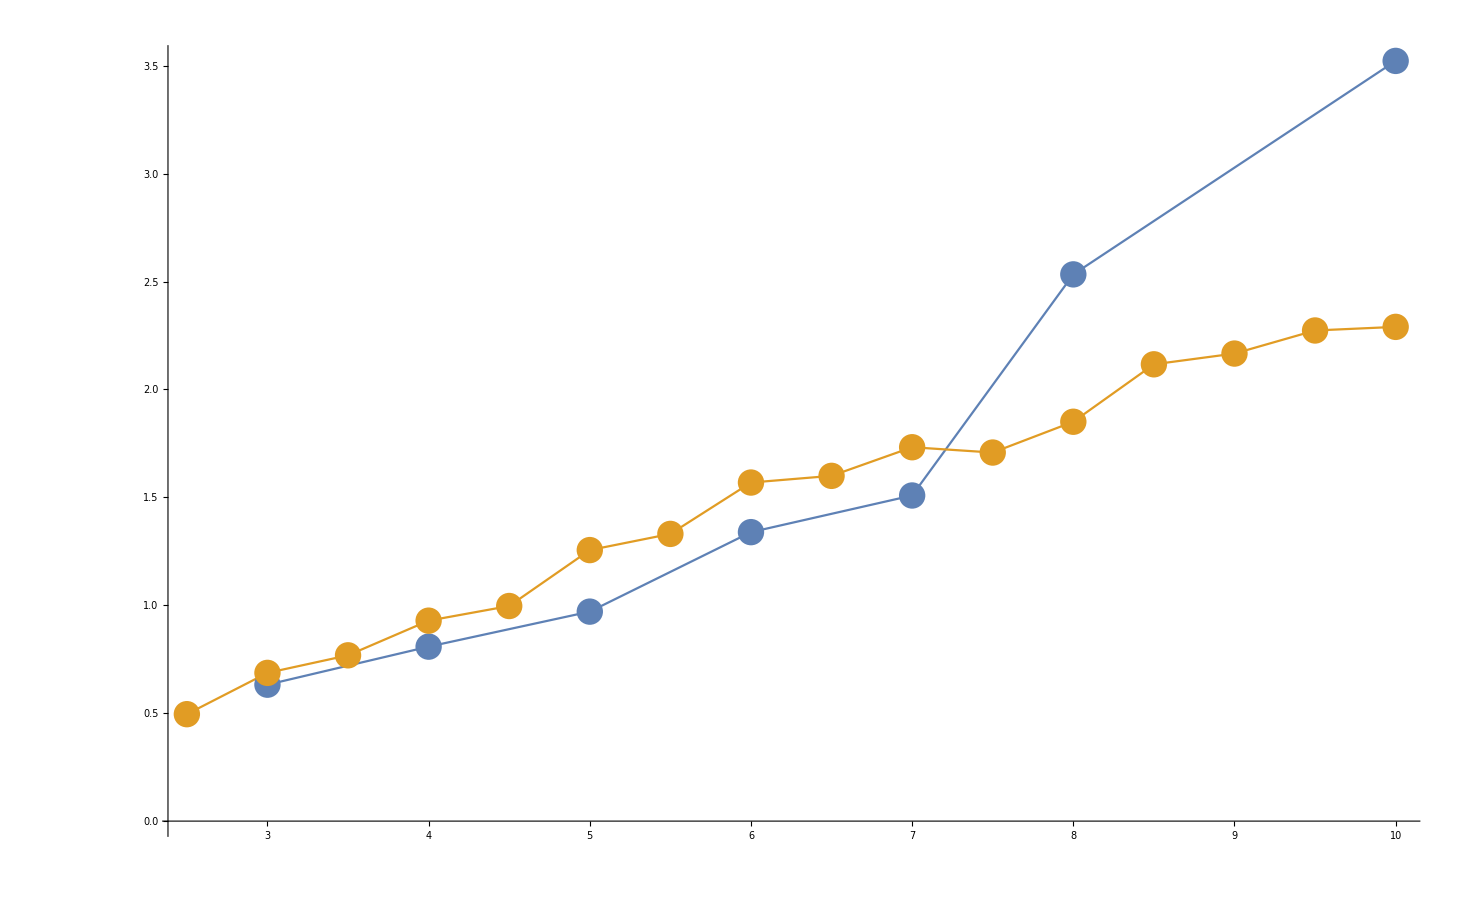

```mathematica
toplot = Drop[Transpose[{con2,(rates[[All,7]]+rates[[All,8]])/2}],{2,3}];
toplot3 ={#[[1]], (33 #[[4,2]]+33 #[[5,2]])/2}&/@sols;

Show[{ListLinePlot[Sort[#]&/@{toplot,toplot3}],ListPlot[Sort[#]&/@{toplot,toplot3}]}]
```

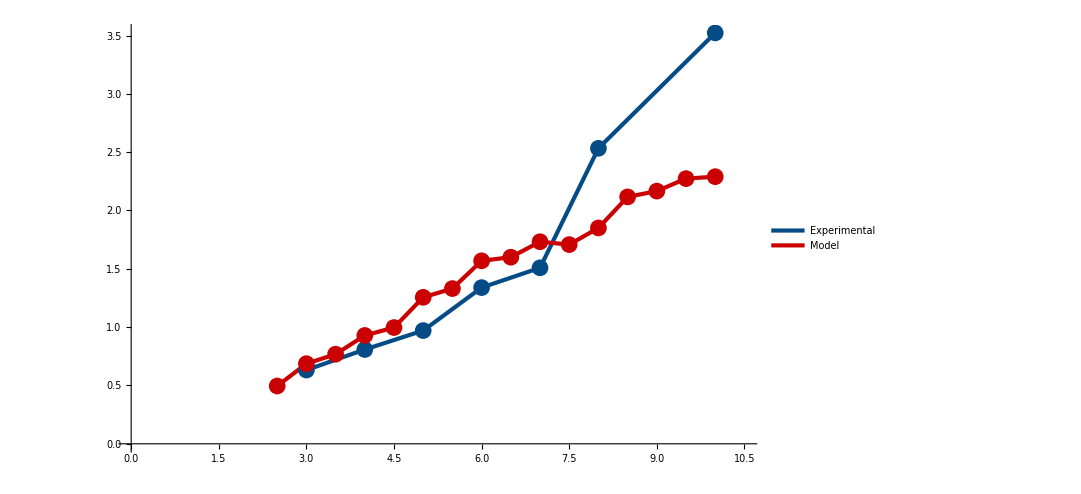
-Graphics-Growth Rate Std. Dev. (nm/s)Concentration (nM)

```mathematica
toout = Labeled[Show[{ListLinePlot[Sort[#]&/@{toplot,toplot3},PlotRange->{{0,10.5},{0,All}},PlotStyle->{{colors[[2]],AbsoluteThickness[3]},{colors[[1]],AbsoluteThickness[3]}},AxesStyle->{{Black,Thick,FontFamily->"Helvetica",Large},{Black,Thick,FontFamily->"Helvetica",Large}},TicksStyle->Black,PlotLegends->Placed[{Style["Experimental",{Black,18,Bold,FontFamily->"Helvetica"}],Style["Model",{Black,18,Bold,FontFamily->"Helvetica"}]},{{0.25,0.7}}]],ListPlot[Sort[#]&/@{toplot,toplot3},PlotStyle->{{colors[[2]],PointSize[0.015]},{colors[[1]],PointSize[0.015]}}]},ImageSize->800],{Rotate[Style["Growth Rate Std. Dev. (nm/s)",{Black,20,Bold,FontFamily->"Helvetica"}],π/2],Style["Concentration (nM)",{Black,20,Bold,FontFamily->"Helvetica"}]},{Left,Bottom}]
```

```mathematica
Export["C:\\Users\\James_Walsh\\Dropbox\\Tropomyosin_Analysis\\New_Figures\\Modelling\\Model_Growthrate_stddev.eps",toout];
Export["C:\\Users\\James_Walsh\\Dropbox\\Tropomyosin_Analysis\\New_Figures\\Modelling\\Model_Growthrate_stddev.png",toout,ImageResolution->200];
```